```mathematica
Traverse[sets1_]:=Block[{sets,i,j, newset, result={}},
sets=Sort[Map[Sort[#]&,sets1]];
For[i=1,i≤Length[sets],i++,
For[j=i+1,j≤Length[sets],j++,
newset=sets;
newset=Delete[newset,j];
newset=Delete[newset,i];
newset=Append[newset,Sort[Flatten[Join[sets[[i]],sets[[j]]]]]];
newset=Sort[Map[Sort[#]&,newset]];
AppendTo[result, sets->newset];
result=Join[result,Traverse[newset]]
]
];
result
]
```

```mathematica
g1=DeleteDuplicates[Traverse[{{1,5},{2},{3},{4}}]];
```

```mathematica
g2=DeleteDuplicates[Traverse[{{1,4},{2},{3},{5}}]];
```

```mathematica
g3=DeleteDuplicates[Traverse[{{4,5},{2},{3},{1}}]];
```

```mathematica
Intersection[g1,g2,g3]
```

{{{2},{1,3,4,5}}→{{1,2,3,4,5}},{{3},{1,2,4,5}}→{{1,2,3,4,5}},{{2,3},{1,4,5}}→{{1,2,3,4,5}},{{2},{3},{1,4,5}}→{{2},{1,3,4,5}},{{2},{3},{1,4,5}}→{{3},{1,2,4,5}},{{2},{3},{1,4,5}}→{{2,3},{1,4,5}}}

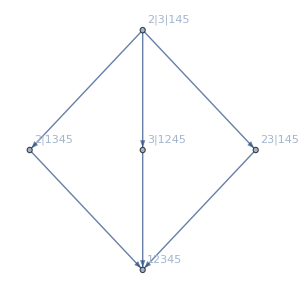

```mathematica
Graph[Intersection[g1,g2,g3],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Map[# ->SymbolToLabel[ SetsToSymbol[#]]&,VertexList[Graph[DeleteDuplicates[Intersection[g1,g2,g3]]]]],
ImageSize->300]
```

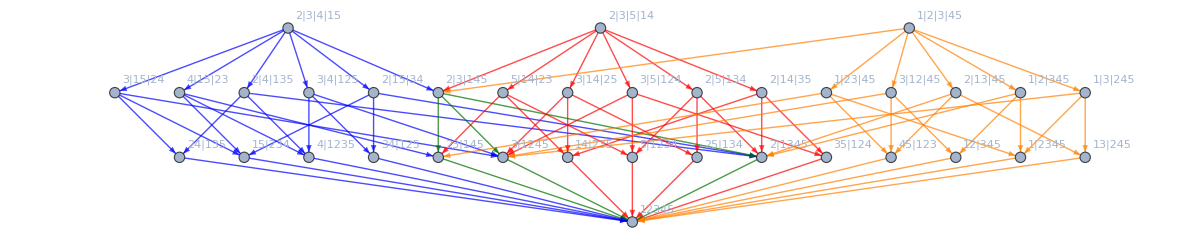

```mathematica
Graph[DeleteDuplicates[Join[g1,g2,g3]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Map[# ->SymbolToLabel[ SetsToSymbol[#]]&,VertexList[Graph[DeleteDuplicates[Join[g1,g2,g3]]]]],
EdgeStyle->Join[
Map[#->Blue&,Select[g1,!MemberQ[Union[g2,g3],#]&]],
Map[#->Red&,Select[g2,!MemberQ[Union[g1,g3],#]&]],
Map[#->Orange&,Select[g3,!MemberQ[Union[g2,g1],#]&]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g2,g3]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g2]],
Map[#->Darker[Darker[Green]]&,Intersection[g3,g2]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g3]]
],
ImageSize->1200]
```

## Not a cycle

```mathematica
g1=DeleteDuplicates[Traverse[{{1,5},{2},{3},{4}}]];
```

```mathematica
g2=DeleteDuplicates[Traverse[{{1,3},{2},{4},{5}}]];
```

```mathematica
g3=DeleteDuplicates[Traverse[{{4,5},{2},{3},{1}}]];
```

```mathematica
Intersection[g1,g2,g3]
```

{{{2},{1,3,4,5}}→{{1,2,3,4,5}}}

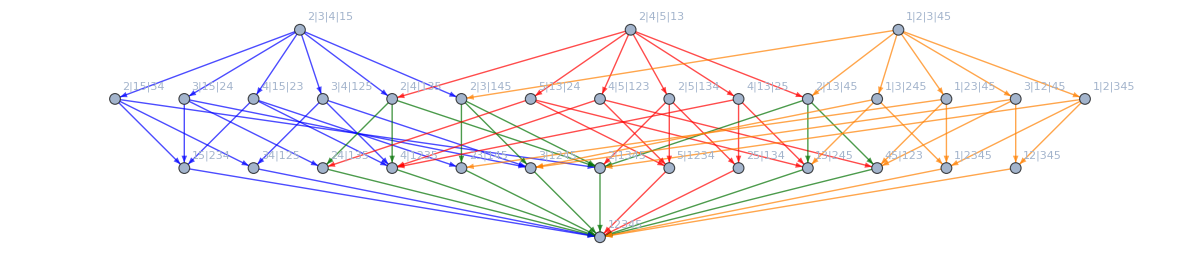

```mathematica
Graph[DeleteDuplicates[Join[g1,g2,g3]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Map[# ->SymbolToLabel[ SetsToSymbol[#]]&,VertexList[Graph[DeleteDuplicates[Join[g1,g2,g3]]]]],
EdgeStyle->Join[
Map[#->Blue&,Select[g1,!MemberQ[Union[g2,g3],#]&]],
Map[#->Red&,Select[g2,!MemberQ[Union[g1,g3],#]&]],
Map[#->Orange&,Select[g3,!MemberQ[Union[g2,g1],#]&]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g2,g3]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g2]],
Map[#->Darker[Darker[Green]]&,Intersection[g3,g2]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g3]]
],
ImageSize->1200]
```

## Two edges

```mathematica
h1=DeleteDuplicates[Traverse[{{1,5},{2},{3},{4}}]];
```

```mathematica
h2=DeleteDuplicates[Traverse[{{2,3},{1},{5},{4}}]];
```

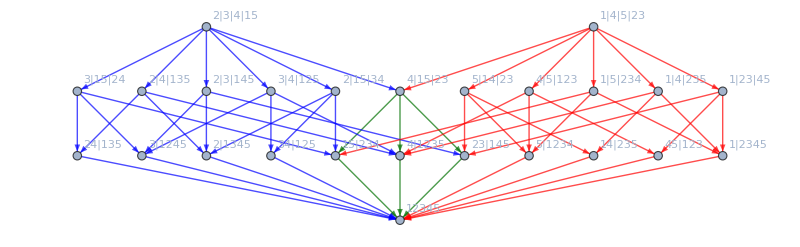

```mathematica
Graph[DeleteDuplicates[Join[h1,h2]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Map[# ->SymbolToLabel[ SetsToSymbol[#]]&,VertexList[Graph[DeleteDuplicates[Join[h1,h2]]]]],
EdgeStyle->Join[
Map[#->Blue&,Select[h1,!MemberQ[h2,#]&]],
Map[#->Red&,Select[h2,!MemberQ[h1,#]&]],
Map[#->Darker[Darker[Green]]&,Intersection[h1,h2]]
],
ImageSize->800]
```

## Two traingles

```mathematica
g1=DeleteDuplicates[Traverse[{{1,5},{2},{3},{4},{6}}]];
```

```mathematica
g2=DeleteDuplicates[Traverse[{{1,4},{2},{3},{5},{6}}]];
```

```mathematica
g3=DeleteDuplicates[Traverse[{{4,5},{2},{3},{1},{6}}]];
```

```mathematica
g4=DeleteDuplicates[Traverse[{{1,3},{2},{5},{4},{6}}]];
```

```mathematica
g5=DeleteDuplicates[Traverse[{{2,3},{4},{1},{5},{6}}]];
```

```mathematica
g6=DeleteDuplicates[Traverse[{{1,2},{5},{3},{4},{6}}]];
```

```mathematica
Intersection[g1,g2,g3]
```

{{{2},{1,3,4,5,6}}→{{1,2,3,4,5,6}},{{3},{1,2,4,5,6}}→{{1,2,3,4,5,6}},{{6},{1,2,3,4,5}}→{{1,2,3,4,5,6}},{{2,3},{1,4,5,6}}→{{1,2,3,4,5,6}},{{2,6},{1,3,4,5}}→{{1,2,3,4,5,6}},{{3,6},{1,2,4,5}}→{{1,2,3,4,5,6}},{{1,4,5},{2,3,6}}→{{1,2,3,4,5,6}},{{2},{3},{1,4,5,6}}→{{2},{1,3,4,5,6}},{{2},{3},{1,4,5,6}}→{{3},{1,2,4,5,6}},{{2},{3},{1,4,5,6}}→{{2,3},{1,4,5,6}},{{2},{6},{1,3,4,5}}→{{2},{1,3,4,5,6}},{{2},{6},{1,3,4,5}}→{{6},{1,2,3,4,5}},{{2},{6},{1,3,4,5}}→{{2,6},{1,3,4,5}},{{2},{3,6},{1,4,5}}→{{2},{1,3,4,5,6}},{{2},{3,6},{1,4,5}}→{{3,6},{1,2,4,5}},{{2},{3,6},{1,4,5}}→{{1,4,5},{2,3,6}},{{3},{6},{1,2,4,5}}→{{3},{1,2,4,5,6}},{{3},{6},{1,2,4,5}}→{{6},{1,2,3,4,5}},{{3},{6},{1,2,4,5}}→{{3,6},{1,2,4,5}},{{3},{2,6},{1,4,5}}→{{3},{1,2,4,5,6}},{{3},{2,6},{1,4,5}}→{{2,6},{1,3,4,5}},{{3},{2,6},{1,4,5}}→{{1,4,5},{2,3,6}},{{6},{2,3},{1,4,5}}→{{6},{1,2,3,4,5}},{{6},{2,3},{1,4,5}}→{{2,3},{1,4,5,6}},{{6},{2,3},{1,4,5}}→{{1,4,5},{2,3,6}},{{2},{3},{6},{1,4,5}}→{{2},{3},{1,4,5,6}},{{2},{3},{6},{1,4,5}}→{{2},{6},{1,3,4,5}},{{2},{3},{6},{1,4,5}}→{{2},{3,6},{1,4,5}},{{2},{3},{6},{1,4,5}}→{{3},{6},{1,2,4,5}},{{2},{3},{6},{1,4,5}}→{{3},{2,6},{1,4,5}},{{2},{3},{6},{1,4,5}}→{{6},{2,3},{1,4,5}}}

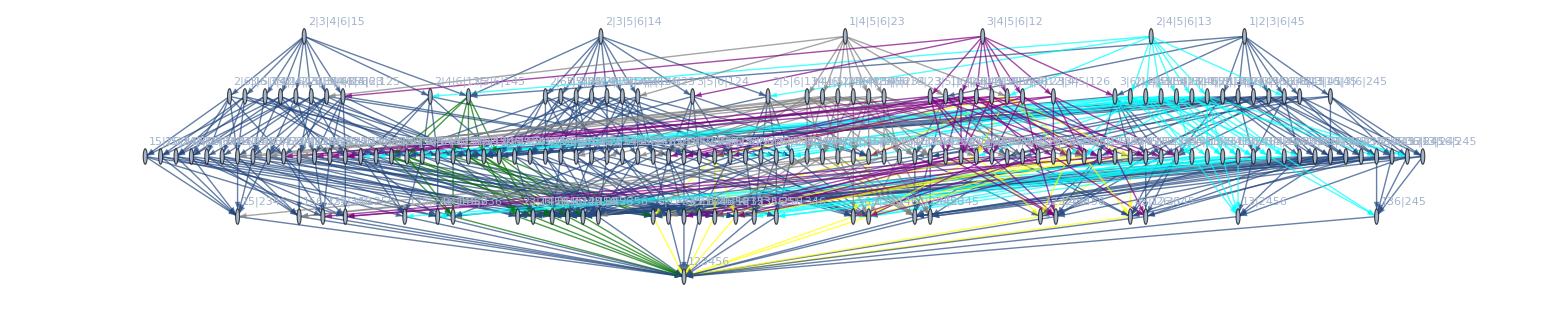

```mathematica
Graph[DeleteDuplicates[Join[g1,g2,g3,g4,g5,g6]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Map[# ->SymbolToLabel[ SetsToSymbol[#]]&,VertexList[Graph[DeleteDuplicates[Join[g1,g2,g3,g4,g5,g6]]]]],
EdgeStyle->Join[
Map[#->Darker[Darker[Green]]&,Intersection[g1,g2,g3]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g2]],
Map[#->Darker[Darker[Green]]&,Intersection[g3,g2]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g3]]

,
Map[#->Cyan&,Select[g4,!MemberQ[Union[g5,g6,g1,g2,g3],#]&]],
Map[#->Gray&,Select[g5,!MemberQ[Union[g4,g6,g1,g2,g3],#]&]],
Map[#->Purple&,Select[g6,!MemberQ[Union[g5,g4,g1,g2,g3],#]&]],
Map[#->Yellow&,Intersection[g4,g5,g6]],
Map[#->Yellow&,Intersection[g4,g5]],
Map[#->Yellow&,Intersection[g6,g5]],
Map[#->Yellow&,Intersection[g4,g6]]
],
ImageSize->1600]
```

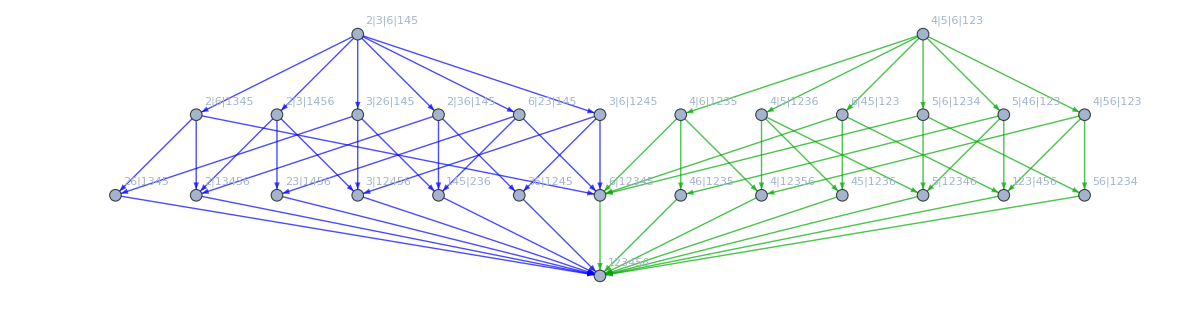

```mathematica
Graph[DeleteDuplicates[Join[Intersection[g1,g2,g3],Intersection[g4,g5,g6]]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Map[# ->SymbolToLabel[ SetsToSymbol[#]]&,VertexList[Graph[DeleteDuplicates[Join[Intersection[g1,g2,g3],Intersection[g4,g5,g6]]]]]],
EdgeStyle->Join[
Map[#->Blue&,Intersection[g1,g2,g3]],
Map[#->Darker[Green]&,Intersection[g4,g5,g6]]
],
ImageSize->1200]
```

## Two triangles not related

```mathematica
g1=DeleteDuplicates[Traverse[{{1,5},{2},{3},{4},{6}}]];
```

```mathematica
g2=DeleteDuplicates[Traverse[{{1,4},{2},{3},{5},{6}}]];
```

```mathematica
g3=DeleteDuplicates[Traverse[{{4,5},{2},{3},{1},{6}}]];
```

```mathematica
g4=DeleteDuplicates[Traverse[{{2,3},{6},{5},{4},{1}}]];
```

```mathematica
g5=DeleteDuplicates[Traverse[{{2,6},{4},{1},{5},{3}}]];
```

```mathematica
g6=DeleteDuplicates[Traverse[{{6,2},{5},{3},{4},{1}}]];
```

```mathematica
Intersection[g1,g2,g3]
```

{{{2},{1,3,4,5,6}}→{{1,2,3,4,5,6}},{{3},{1,2,4,5,6}}→{{1,2,3,4,5,6}},{{6},{1,2,3,4,5}}→{{1,2,3,4,5,6}},{{2,3},{1,4,5,6}}→{{1,2,3,4,5,6}},{{2,6},{1,3,4,5}}→{{1,2,3,4,5,6}},{{3,6},{1,2,4,5}}→{{1,2,3,4,5,6}},{{1,4,5},{2,3,6}}→{{1,2,3,4,5,6}},{{2},{3},{1,4,5,6}}→{{2},{1,3,4,5,6}},{{2},{3},{1,4,5,6}}→{{3},{1,2,4,5,6}},{{2},{3},{1,4,5,6}}→{{2,3},{1,4,5,6}},{{2},{6},{1,3,4,5}}→{{2},{1,3,4,5,6}},{{2},{6},{1,3,4,5}}→{{6},{1,2,3,4,5}},{{2},{6},{1,3,4,5}}→{{2,6},{1,3,4,5}},{{2},{3,6},{1,4,5}}→{{2},{1,3,4,5,6}},{{2},{3,6},{1,4,5}}→{{3,6},{1,2,4,5}},{{2},{3,6},{1,4,5}}→{{1,4,5},{2,3,6}},{{3},{6},{1,2,4,5}}→{{3},{1,2,4,5,6}},{{3},{6},{1,2,4,5}}→{{6},{1,2,3,4,5}},{{3},{6},{1,2,4,5}}→{{3,6},{1,2,4,5}},{{3},{2,6},{1,4,5}}→{{3},{1,2,4,5,6}},{{3},{2,6},{1,4,5}}→{{2,6},{1,3,4,5}},{{3},{2,6},{1,4,5}}→{{1,4,5},{2,3,6}},{{6},{2,3},{1,4,5}}→{{6},{1,2,3,4,5}},{{6},{2,3},{1,4,5}}→{{2,3},{1,4,5,6}},{{6},{2,3},{1,4,5}}→{{1,4,5},{2,3,6}},{{2},{3},{6},{1,4,5}}→{{2},{3},{1,4,5,6}},{{2},{3},{6},{1,4,5}}→{{2},{6},{1,3,4,5}},{{2},{3},{6},{1,4,5}}→{{2},{3,6},{1,4,5}},{{2},{3},{6},{1,4,5}}→{{3},{6},{1,2,4,5}},{{2},{3},{6},{1,4,5}}→{{3},{2,6},{1,4,5}},{{2},{3},{6},{1,4,5}}→{{6},{2,3},{1,4,5}}}

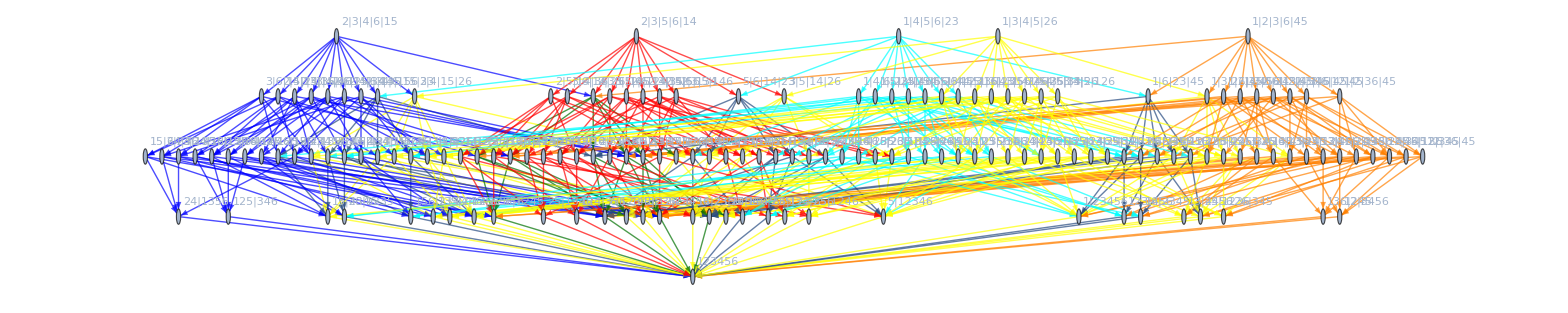

```mathematica
Graph[DeleteDuplicates[Join[g1,g2,g3,g4,g5,g6]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Map[# ->SymbolToLabel[ SetsToSymbol[#]]&,VertexList[Graph[DeleteDuplicates[Join[g1,g2,g3,g4,g5,g6]]]]],
EdgeStyle->Join[
Map[#->Blue&,Select[g1,!MemberQ[Union[g2,g3,g4,g5,g6],#]&]],
Map[#->Red&,Select[g2,!MemberQ[Union[g1,g3,g4,g5,g6],#]&]],
Map[#->Orange&,Select[g3,!MemberQ[Union[g2,g1,g4,g5,g6],#]&]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g2,g3]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g2]],
Map[#->Darker[Darker[Green]]&,Intersection[g3,g2]],
Map[#->Darker[Darker[Green]]&,Intersection[g1,g3]]

,
Map[#->Cyan&,Select[g4,!MemberQ[Union[g5,g6,g1,g2,g3],#]&]],
Map[#->Gray&,Select[g5,!MemberQ[Union[g4,g6,g1,g2,g3],#]&]],
Map[#->Purple&,Select[g6,!MemberQ[Union[g5,g4,g1,g2,g3],#]&]],
Map[#->Yellow&,Intersection[g4,g5,g6]],
Map[#->Yellow&,Intersection[g4,g5]],
Map[#->Yellow&,Intersection[g6,g5]],
Map[#->Yellow&,Intersection[g4,g6]]
],
ImageSize->1600]
```

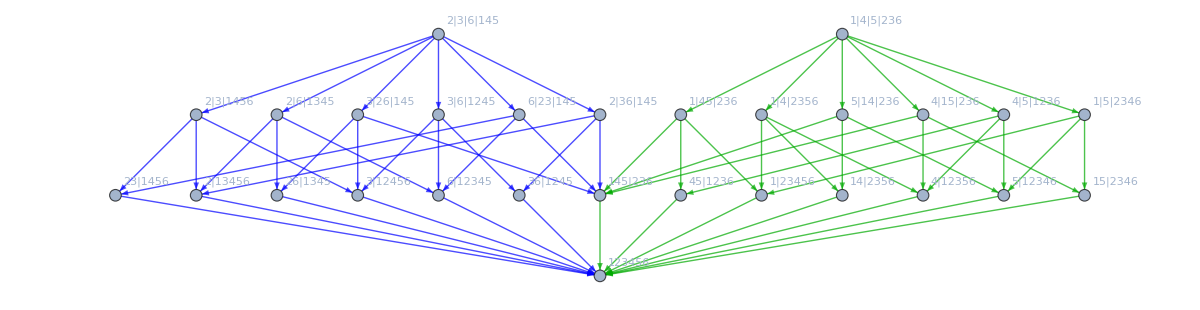

```mathematica
Graph[DeleteDuplicates[Join[Intersection[g1,g2,g3],Intersection[g4,g5,g6]]],
GraphLayout->"LayeredDigraphEmbedding",
VertexLabels->Map[# ->SymbolToLabel[ SetsToSymbol[#]]&,VertexList[Graph[DeleteDuplicates[Join[Intersection[g1,g2,g3],Intersection[g4,g5,g6]]]]]],
EdgeStyle->Join[
Map[#->Blue&,Intersection[g1,g2,g3]],
Map[#->Darker[Green]&,Intersection[g4,g5,g6]]
],
ImageSize->1200]
```

```mathematica
Table[allGraphs5[k,"graph"],{k,Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5&&MaximalPlanarQ[g]]&]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Summ
```

Summ

```mathematica
Table[Labeled[allGraphs6[k,"graph"],k],{k,Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},VertexCount[g]==6&&MaximalPlanarQ[g]]&]}]
```

{-Graphics-7174416,-Graphics-7174414,-Graphics-7174368,-Graphics-7174360,-Graphics-7174342,-Graphics-7174336,-Graphics-7174206,-Graphics-7174200,-Graphics-7174182,-Graphics-7174174,-Graphics-7174128,-Graphics-7174126,-Graphics-7173714,-Graphics-7173712,-Graphics-7173642,-Graphics-7173616,-Graphics-7173478,-Graphics-7173454,-Graphics-7172262,-Graphics-7172254,-Graphics-7172238,-Graphics-7172158,-Graphics-7172014,-Graphics-7171942,-Graphics-7171534,-Graphics-7171528,-Graphics-7171510,-Graphics-7171456,-Graphics-7167888,-Graphics-7167882,-Graphics-7167862,-Graphics-7167802,-Graphics-7167622,-Graphics-7167568,-Graphics-7167162,-Graphics-7167154,-Graphics-7167136,-Graphics-7166920,-Graphics-7165704,-Graphics-7165702,-Graphics-7165624,-Graphics-7165462,-Graphics-7154742,-Graphics-7154740,-Graphics-7154688,-Graphics-7154680,-Graphics-7154524,-Graphics-7154518,-Graphics-7154040,-Graphics-7154038,-Graphics-7153960,-Graphics-7153798,-Graphics-7152582,-Graphics-7152574,-Graphics-7152556,-Graphics-7152340,-Graphics-7148206,-Graphics-7148200,-Graphics-7148182,-Graphics-7148128,-Graphics-7115394,-Graphics-7115392,-Graphics-7115322,-Graphics-7115296,-Graphics-7115158,-Graphics-7115134,-Graphics-7113216,-Graphics-7112974,-Graphics-7112488,-Graphics-7108840,-Graphics-7108762,-Graphics-7108114,-Graphics-7095712,-Graphics-7095694,-Graphics-7094992,-Graphics-6997302,-Graphics-6997294,-Graphics-6997278,-Graphics-6997198,-Graphics-6997054,-Graphics-6996982,-Graphics-6996576,-Graphics-6996334,-Graphics-6994390,-Graphics-6990736,-Graphics-6990718,-Graphics-6988558,-Graphics-6977620,-Graphics-6977542,-Graphics-6975436,-Graphics-6938254,-Graphics-6938248,-Graphics-6938230,-Graphics-6938176,-Graphics-6937528,-Graphics-6936070,-Graphics-6643008,-Graphics-6643002,-Graphics-6642982,-Graphics-6642922,-Graphics-6642742,-Graphics-6642688,-Graphics-6642280,-Graphics-6642202,-Graphics-6640816,-Graphics-6640798,-Graphics-6635722,-Graphics-6634264,-Graphics-6623328,-Graphics-6623086,-Graphics-6616768,-Graphics-6583962,-Graphics-6583954,-Graphics-6583936,-Graphics-6583720,-Graphics-6583234,-Graphics-6577402,-Graphics-6465864,-Graphics-6465862,-Graphics-6465784,-Graphics-6465622,-Graphics-6463678,-Graphics-6459304,-Graphics-5580102,-Graphics-5580100,-Graphics-5580048,-Graphics-5580040,-Graphics-5579884,-Graphics-5579878,-Graphics-5579392,-Graphics-5579374,-Graphics-5577940,-Graphics-5577862,-Graphics-5573568,-Graphics-5573326,-Graphics-5559718,-Graphics-5558260,-Graphics-5553886,-Graphics-5521080,-Graphics-5521078,-Graphics-5521000,-Graphics-5520838,-Graphics-5520352,-Graphics-5501398,-Graphics-5402982,-Graphics-5402974,-Graphics-5402956,-Graphics-5402740,-Graphics-5400796,-Graphics-5383300,-Graphics-5048686,-Graphics-5048680,-Graphics-5048662,-Graphics-5048608,-Graphics-5042128,-Graphics-5029006,-Graphics-2391448,-Graphics-2391400,-Graphics-2391240,-Graphics-2390754,-Graphics-2390752,-Graphics-2390728,-Graphics-2389296,-Graphics-2389288,-Graphics-2389216,-Graphics-2384920,-Graphics-2384914,-Graphics-2384680,-Graphics-2371774,-Graphics-2371720,-Graphics-2371558,-Graphics-2332434,-Graphics-2332432,-Graphics-2332408,-Graphics-2330248,-Graphics-2325874,-Graphics-2312752,-Graphics-2214336,-Graphics-2214328,-Graphics-2214256,-Graphics-2213608,-Graphics-2207776,-Graphics-2194654,-Graphics-1860040,-Graphics-1860034,-Graphics-1859800,-Graphics-1859314,-Graphics-1857856,-Graphics-1840360,-Graphics-797134,-Graphics-797080,-Graphics-796918,-Graphics-796432,-Graphics-794974,-Graphics-790600}

```mathematica
SummaryPrintGood5[29523]
```

SummaryPrintGood5[29523]